```mathematica
(*Supplementary material to Experimental investigation on backflow of power-law fluids in planar
fractures, by A.Lenci, L.Chiapponi, S.Longo, and V.Di Federico*)

(*Backflow in planar geometry, with leakage, for power-law fluid*)

(*Solution with parametric integration in space and integration in time*)
(*functionalized constructs as an alternative to ParametricNDSolve, which allows to handle the parameters for the initial conditions*)

(*parametric solution of the equation in in P(X,T)*)
solp[LL_?NumericQ,LL2_?NumericQ,H_?NumericQ,nn_?NumericQ,Hnew_?NumericQ,Hp_?NumericQ,deltaT_?NumericQ]:=solp[x]=P/.First[NDSolve[{-LL*H*P[x]^(1/nn)-LL2*P[x]^(1/nn)+H^((2*nn+1)/nn)P'[x]^((1-nn)/nn)*P''[x]==(Hnew-Hp)/deltaT,P'[1]==0,P[0]==0},P,{x,0,1}]];
(*parametric evaluation of the integral of P(X,T) in the domain [0,1]*)
integral[LL_?NumericQ,LL2_?NumericQ,H_?NumericQ,nn_?NumericQ,Hnew_?NumericQ,Hp_?NumericQ,deltaT_?NumericQ]:=
NIntegrate[solp[LL,LL2,H,nn,Hnew,Hp,deltaT][xx],{xx,0,1}];

(*parametric evaluation of P(X,T) after completing the time integration. It is necessary to insert the value of the thickness H and of its time derivative at the time of representation*)
solpfin[LL_?NumericQ,LL2_?NumericQ,H_?NumericQ,nn_?NumericQ,Hpunto_?NumericQ]:=
solpfin[xx]=PP/.First[NDSolve[{-LL*H*PP[x]^(1/nn)-LL2*PP[x]^(1/nn)+H^((2*nn+1)/nn)PP'[x]^((1-nn)/nn)*PP''[x]==Hpunto,PP'[1]==0,PP[0]==0},PP,{x,0,1}]];

(*inverse theoretical solution for H(T) without leakage*)
solVitHT[H_,n_,Pe_,λ_]:=1/((2+n)^(1/n)*(1+n+λ))*(Hypergeometric2F1[1/n,1/n+(1+n)/(n λ),((1+n)(1+λ))/(n λ),H^-λ Pe]/H^((1+n+λ)/n) - Hypergeometric2F1[1/n,1/n+(1+n)/(n λ),((1+n)(1+λ))/(n λ),Pe]); 
(*Direct theoretical solution for H(T) without leakage*)
HT[n_?NumericQ,Pe_?NumericQ,λ_?NumericQ]:=Function[{t},Re[H/.FindRoot[Abs[solVitHT[H,n,Pe,λ]-t],{H,1}]]];
```

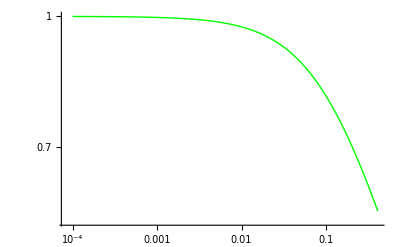

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

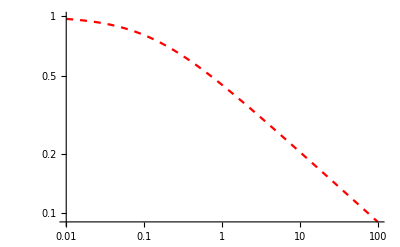

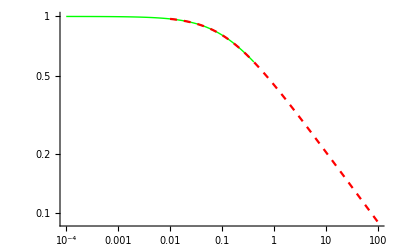

```mathematica
LL=0.0; (*lateral leakage coefficient*)
LL2=0.; (*diffuse leakage coefficient*)

begin=1; (*start counter*)
end=500; (*end counter*)
deltatt=0.01; (*standard size of the time step*)
H0=1.; (*initial condition for the fracture thickness*)

n=1.;
λ=0.8;
Pe=0.;
F0=0.;

tempo=0.;
Hsol=H0;
Hsolim=0.;
time=0;

For[pp=begin,pp≤end,pp=pp+1,
(*adapting initial size of time step to follow rapid initial variation of H*)
deltat1=If[pp<101,deltatt/100,deltatt/10];

deltat=If[ pp>500,deltatt,deltat1];

deltat=If[time>100,deltat*10,deltat];

deltat=If[time>500,deltat*10,deltat];

time=time+deltat;

(*forcing the vertical balance by equating the integral of pressure, with the free parameter HH, to the elastic reaction of the walls plus the contributions by Pe and F0*)
Hpp1=FindRoot[integral[LL,LL2,(HH+H0)/2,n,HH,H0,deltat]==((HH+H0)/2)^λ-Pe+F0,{HH,H0}][[1]][[2]];
Hp=Re[Hpp1];

Hsol=Flatten[{Hsol,Hp}];
tempo=Flatten[{tempo,time}];
Hsolim=Flatten[{Hsolim,Im[Hpp1]}];
H0=Hp
];
(*interpolating output for further processing*)
ifun = Interpolation[Transpose[{tempo,Hsol}]];
HHH[T_]:=ifun[T];
DHHH[TT_]:=ifun'[T]/.T->TT;

(*time derivative of H is the outflow rate*)
Vel=-DHHH/@ tempo;

(*plotting the numerical solution*)
plnum=ListLogLogPlot[Transpose[{tempo,Hsol}],Joined->True,PlotRange->All,PlotStyle->{Thick,Green}]

(*plotting the solution without leakage, for L=0. and LL=0., for comparison*)
plref=LogLogPlot[HT[n,Pe-F0,λ][T],{T,0.01,100},PlotStyle->{Red, Dashed}]

Show[plnum,plref,PlotRange->All]
```